```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/jam/Kuweta/notatki/programming/mathematica/rand_file/usage_examples

```mathematica
<<RandFile`
```

Package RandFile version 0.0.17 (last modification: 25/01/2013).

Usage notes:

1) Almost all provided functions require to set a global variable pointing to file with random data! This can be done by using SetTrueRandomDataFile function. For example SetTrueRandomDataFile["/home/user/data/random_file.bin"]. Please mind that it is advised to use this function only once during session.

2) If you intend to use TrueRandomSequence function you must use SetMaxTrueRandomSequenceLength and declare at least one sequence. Currently declared sequences can be displayed by calling GetTrueRandomDataMarkers[]. Once defined, the used maximal length cannot be changed during the session.

```mathematica
intensity[tetha_,Amp_,k_,d_,a_]:=Amp*((Sin[0.5 k a* Sin[tetha]]/(0.5 k a* Sin[tetha]))^2)*((Cos[0.5 k d *Sin[tetha]])^2);
```

```mathematica
myLambda=680*10^-6;
myA=1;
myD=5;
```

```mathematica
calcDisp[dataFile_String]:=Block[{M=101,t=10,d=myD,a=myA,lambda=myLambda,maxangle,detectorsize,pprev,p,k,n,S,q,phase,path,alfa,beta,tetha,gamma,source,position,angle,temp1,temp2,temp3,temp4,temp5,Disp},
SetTrueRandomDataFile[dataFile];
If[d<a+0.5,d=a+0.5];
maxangle=90Pi/180;
detectorsize=Pi/M;
p=Table[{0,0},{M}];
pprev=Table[{0,0},{M}];
S=Table[{N[180/Pi(-Pi/2+(i-0.5)*detectorsize)],0},{i,1,M}];
Disp=S;
gamma=Table[0.05,{M}];
q = Table[TrueRandomReal[{0,1}],{M}];
n=0;
alfa=0.999;
beta=0.9;

Do[
source=TrueRandomInteger[{1,2}];
position=TrueRandomReal[{0,a*lambda}];
angle=TrueRandomReal[{-maxangle,maxangle}];

y=(-1)^(source+1)((d-a)/2*lambda+position);

temp1=y;
temp2=temp1*temp1;
temp3=Sin[angle];
temp4=Cos[angle]^2;
temp5=temp1*temp4+temp3*Sqrt[1-temp2*temp4];
tetha=ArcSin[temp5];

k=Ceiling[(tetha+Pi/2)/detectorsize];
path=Sqrt[1-2*temp1*temp5];
phase=2 Pi path/lambda;

n=n+1;
pprev[[k]]=p[[k]];

p[[k,1]]=gamma[[k]]*p[[k,1]]+(1-gamma[[k]])*Cos[phase];
p[[k,2]]=gamma[[k]]*p[[k,2]]+(1-gamma[[k]])*Sin[phase];

q[[k]]=beta*q[[k]]+(1-beta )0.5Sqrt[(p[[k,1]]-pprev[[k,1]])^2+(p[[k,2]]-pprev[[k,2]])^2];
gamma[[k]]=alfa*(1-q[[k]]);

If[p[[k,1]]^2+p[[k,2]]^2≥TrueRandomReal[{0,1}],
S[[k,2]]=S[[k,2]]+1;
Disp[[All,2]]=S[[All,2]]/Max[S[[All,2]]]
];,{j,0,150000}
];
CloseTrueRandomDataFile[];
Disp
];
```

```mathematica
disp=calcDisp["dseSample1.bin"];
```

Using file "dseSample1.bin" which contains 2097152 bytes of data.

```mathematica
Export["resDSESample7.dat",disp]
```

resDSESample7.dat

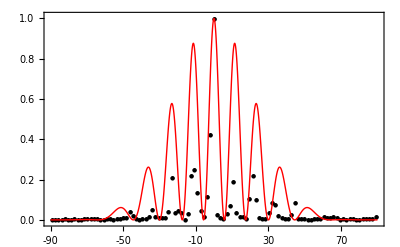

```mathematica
plotDES=Show[{ListPlot[disp,Frame->{{True,False},{True,False}},PlotStyle->Black,PlotMarkers->{Automatic,6},AxesOrigin -> {-90,0},PlotRange->{{-90,90},{-0.01,1.01}},FrameTicks->{{Automatic,None},{{-90,-80,-70,-60,-50,-40,-30,-20,-10,0,10,20,30,40,50,60,70,80,90},None}}],Plot[intensity[x Pi/180,1,(2Pi/myLambda),(myD*myLambda),myA*myLambda],{x,-90,90},AxesOrigin -> {-90,0},PlotStyle->{Red},PlotRange->{{-90,90},{0,1}}, PerformanceGoal->"Quality"]
},ImageSize->400]
```

```mathematica
Export["plotDSESample1.pdf",plotDES]
```

plotDSESample1.pdf